{ψ→ParametricFunction[<>]}

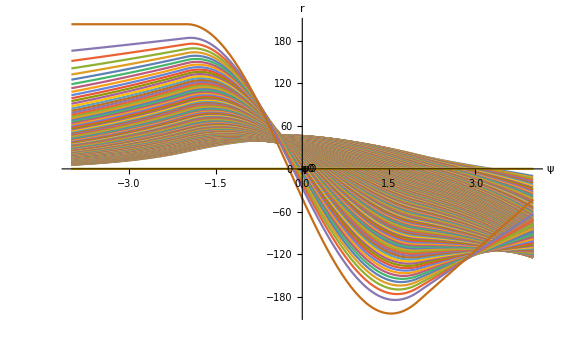

```mathematica
V0=-3;a=2;α=0.262713;ψ0=10^-3;x0=2a;
V[x_]:=Which[Abs[x]≤a,V0,True,0]
sol=
Block[{ψ,x,x1=-x0,x2=x0},
ParametricNDSolve[{ψ''[x]+α(e-V[x])ψ[x]==0,ψ[x1]==ψ0,ψ'[x1]==√(-α(e-V[x1]))  ψ0},
ψ,{x,x1,x2},e]]
Plot[{Evaluate[Table[(ψ[e][r]/.sol)/NIntegrate[(ψ[e][r]/.sol)^2,{r,-x0,x0}],{e,-2,0,.01}]],ψ0,-ψ0},{r,-x0,x0},
PlotRange->All(*{{-4.,6.},{-0.01,0.005}}*),
AxesLabel->{"ψ","r"},
Epilog->{Text["ψ0",{0.1,ψ0}],Text["-ψ0",{0.1,-ψ0}]},
PlotStyle->Table[Table[{m,n,0},{n,0,1,.01}],{m,0,1,.01}],PlotPoints->100]
Clear["Global`*"]
```